# Ordinary Differential Equations and Dynamical Systems with Mathematica

©2001-2008 by Gerald Teschl  <mailto:Gerald.Teschl@univie.ac.at>, <http://www.mat.univie.ac.at/~gerald/>

### First order equations

This command will illustrate the vector field corresponding to a given equation.

```mathematica
Needs["VectorFieldPlots`"];
```

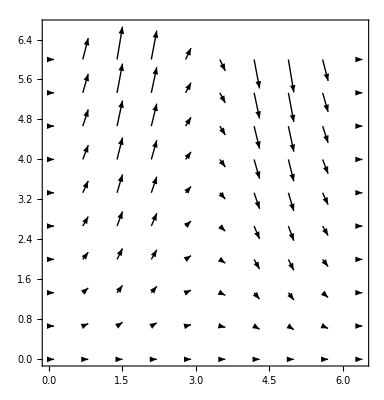

```mathematica
VectorFieldPlot[{1,x Sin[t]},{t,0,2 π},{x,0,6},Frame->True,PlotPoints->10]
```

Now here is the general solution of this equation.

```mathematica
DSolve[x'[t]==x[t] Sin[t],x[t],t]
```

{{x[t]→ⅇ^(-Cos[t]) C[1]}}

And here is the solution of the initial value problem.

```mathematica
DSolve[{x'[t]==x[t] Sin[t],x[0]==1},x[t],t]
```

{{x[t]→ⅇ^(1-Cos[t])}}

Here is how it looks like.

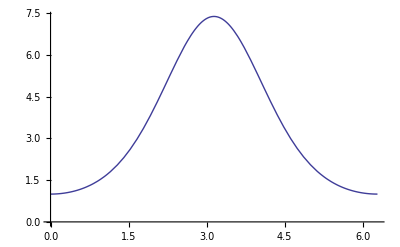

```mathematica
Plot[x[t]/.%,{t,0,2 π}]
```

Only one solution is found here:

```mathematica
DSolve[{x'[t]==√x[t],x[0]==0},x[t],t]
```

{{x[t]→t^2/4}}

The first "solution" is no solution!

```mathematica
DSolve[{x'[t]==√x[t],x[0]==x0},x[t],t]//Simplify
```

{{x[t]→1/4 (t-2 √x0)^2},{x[t]→1/4 (t+2 √x0)^2}}

It satisfies x'[t]==-√x[t]

### Qualitative analysis

```mathematica
NDSolve[{x'[t]==x[t]^2-t^2,x[0]==1},x[t],{t,-2,2}]
```

NDSolve::ndsz: At t == 1.03749, step size is effectively zero; singularity or stiff system suspected.

{{x[t]→InterpolatingFunction[{{-2.,1.03749}},<>][t]}}

For the PhasePlot commad see section "Planar dynamical systems" below.

```mathematica
PhasePlot[{1,y^2-x^2},{{0,-2},{0,-2},{1,-1.5},{0,-1.25},{0,-0.75},{0,-0.676},{0,-0.5},{0,-0.25},{0,0},{0,0.1},{0,0.25},{0,0.5},{0,0.676},{0,0.75},{-1,1.5},{0,2},{1,1},{-1,-1},{1.5,1.5},{-1.5,-1.5},{2,2},{-2,-2},{-1.8,2.3},{1.8,-2.3},{3,2.1},{-3,-2.1}},3,PlotRange->{{-4,4},{-3,3}},AxesLabel->{"t","x"}]
```

```mathematica
xp[t_]=t; ym[t_]=√(2+t^2);
x1[t_]= x[t] /.Flatten[NDSolve[{x'[t]==x[t]^2-t^2,x[0.5]==xp[0.5]},x[t],{t,0,1.2}]];
x2[t_]= x[t] /.Flatten[NDSolve[{x'[t]==x[t]^2-t^2,x[0.5]==ym[0.5]},x[t],{t,0,1.2}]];
```

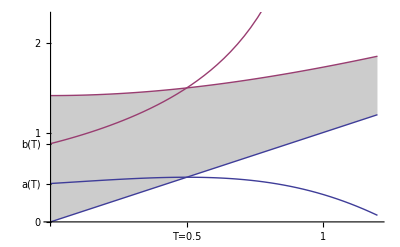

```mathematica
gr1=Plot[{xp[t],ym[t]},{t,0,1.2},Filling->{1->{{2},GrayLevel[0.8]}}];
gr2=Plot[{x1[t],x2[t]},{t,0,1.2}];Show[gr1,gr2,Ticks->{{{0.5,"T=0.5"},1,1.5},{0,{x1[0],"a(T)"},{x2[0],"b(T)"},1,2}},PlotRange->{0,2.3}]
```

### The contraction principle

Iteration of a function:

```mathematica
ShowWeb[K_,xstart_,nmax_]:=Block[{x,xmin,xmax,graph,web},
x[0]:= xstart;
x[n_]:=x[n]=K[x[n-1]];
If[x[0]==x[1],Return[Print[Fixed Point!]]];
web=Flatten[Table[{{x[n],x[n]},{x[n],x[n+1]}},{n,0,nmax}],1];
xmax=Max[web]; xmin=Min[web];
graph= Plot[{K[x],x},{x,xmin,xmax},DisplayFunction->Identity];
Show[graph,Graphics[Line[web]],DisplayFunction->$DisplayFunction]
] /; (IntegerQ[nmax] && Positive[nmax])
```

```mathematica
ShowWeb[(1-#^2/2)&,0,12];
```

```mathematica
ShowWeb[-2ArcTan[#]&,1,12];
```

Animation

```mathematica
ShowWebArray[K_,xstart_,nmax_]:=Block[{i,x,xmin,xmax,graph,web},
x[0]:= xstart;
x[n_]:=x[n]=K[x[n-1]];
If[x[0]==x[1],Return[Print[Fixed Point!]]];
web=Flatten[Table[{{x[n],x[n]},{x[n],x[n+1]}},{n,0,nmax}],1];
xmax=Max[web];
xmin=Min[web];
graph= Plot[{K[x],x},{x,xmin,xmax},DisplayFunction->Identity];
Do[Show[graph,Graphics[Line[Take[web,i]]],DisplayFunction->$DisplayFunction],{i,1,Length[web]}]
] /; (IntegerQ[nmax] && Positive[nmax])
```

Select the cell containing all grapics and then choose "Animate Selected Graphics" from the "Cell" menu.

```mathematica
ShowWebArray[(1-#^2/2)&,0,10];
```

### Picard iteration

```mathematica
f[t_,x_]=1/(1-x);x0=0;
```

```mathematica
x[0,t_]=x0;
x[n_,t_]:=x0+∫_0^t f[s,x[n-1,s]]ⅆs;
```

```mathematica
Series[x[2,t],{t,0,2}]
```

t+t^2/2+O[t]^3

```mathematica
Series[x[t] /. DSolve[{x'[t]==f[t,x[t]],x[0]==x0},x[t],t][[1]],{t,0,2}]//FullSimplify
```

t+t^2/2+O[t]^3

### Linear systems

The Joran decomposition of a matrix

```mathematica
A=({{-11, -35, -24}, {-1, -1, -2}, {8, 22, 17}});
```

```mathematica
{U,J}=JordanDecomposition[A];
J // MatrixForm
```

(1 | 0 | 0
0 | 2 | 1
0 | 0 | 2)

```mathematica
A==U.J.Inverse[U]
```

True

```mathematica
MatrixExp[t J] //MatrixForm
```

(ⅇ^t | 0 | 0
0 | ⅇ^(2 t) | ⅇ^(2 t) t
0 | 0 | ⅇ^(2 t))

The real Joran decomposition of a matrix

```mathematica
A=({{2, -1, -1, 0}, {1, 0, 0, -1}, {1, 0, 2, -1}, {0, 1, 1, 0}});
```

```mathematica
{U,J}=JordanDecomposition[A];
J // MatrixForm
```

(1-ⅈ | 1 | 0 | 0
0 | 1-ⅈ | 0 | 0
0 | 0 | 1+ⅈ | 1
0 | 0 | 0 | 1+ⅈ)

```mathematica
U // MatrixForm
```

(-ⅈ | -ⅈ | ⅈ | ⅈ
-ⅈ | 0 | ⅈ | 0
1 | 1 | 1 | 1
1 | 0 | 1 | 0)

```mathematica
TU=Transpose[U];
V=Transpose[{Re[TU[[1]]],Im[TU[[1]]],Re[TU[[2]]],Im[TU[[2]]]}];
V// MatrixForm
```

(0 | -1 | 0 | -1
0 | -1 | 0 | 0
1 | 0 | 1 | 0
1 | 0 | 0 | 0)

```mathematica
Jr=Inverse[V].A.V;
Jr//MatrixForm
```

(1 | -1 | 1 | 0
1 | 1 | 0 | 1
0 | 0 | 1 | -1
0 | 0 | 1 | 1)

```mathematica
MatrixExp[t Jr]//FullSimplify//MatrixForm
```

(ⅇ^t Cos[t] | -ⅇ^t Sin[t] | ⅇ^t t Cos[t] | -ⅇ^t t Sin[t]
ⅇ^t Sin[t] | ⅇ^t Cos[t] | ⅇ^t t Sin[t] | ⅇ^t t Cos[t]
0 | 0 | ⅇ^t Cos[t] | -ⅇ^t Sin[t]
0 | 0 | ⅇ^t Sin[t] | ⅇ^t Cos[t])

The logarithm of a Jordan block

```mathematica
Nil[n_Integer,m_Integer]:=Table[If[j-i==m,1,0],{i,1,n},{j,1,n}];
Ln[n_Integer]:=Log[α]Nil[n,0]-∑_(j=1)^n (-1)^j/(j α^j)Nil[n,j];
```

```mathematica
Ln[4] //MatrixForm
```

(Log[α] | 1/α | -1/(2 α^2) | 1/(3 α^3)
0 | Log[α] | 1/α | -1/(2 α^2)
0 | 0 | Log[α] | 1/α
0 | 0 | 0 | Log[α])

```mathematica
MatrixExp[Ln[4]] //Simplify //MatrixForm
```

(α | 1 | 0 | 0
0 | α | 1 | 0
0 | 0 | α | 1
0 | 0 | 0 | α)

### Stable Manifold

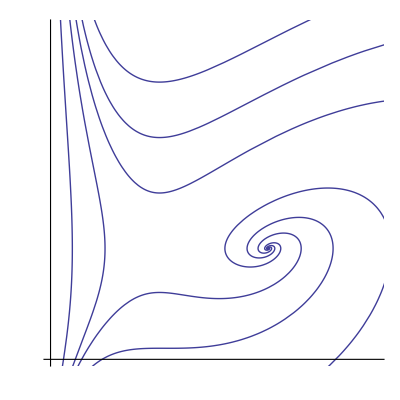

```mathematica
pp1=PhasePlot[{(1-y)x,(1-x)y+(x-1)^2},{{0.2,1},{0.5,1},{1,0.1},{1,1},{1,1.5},{1.6,1},{2.3,1},{1,2},{1,2.5}},12,Ticks->False,PlotRange->{{0,3},{0,3}}]
```

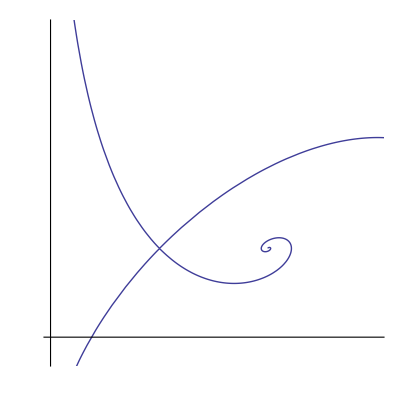

```mathematica
pp2=PhasePlot[{(1-y)x,(1-x)y+(x-1)^2},{{1.02,0.98},{1.02,1.02}},12,Ticks->False,PlotRange->{{0,3},{0,3}}]
```

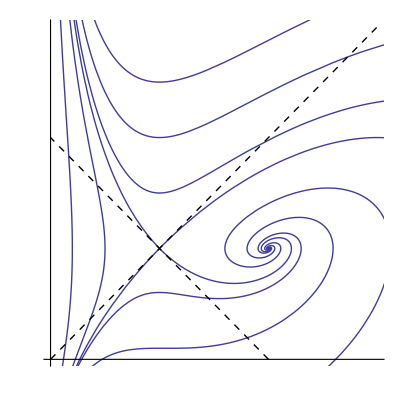

```mathematica
Show[pp1,pp2,Graphics[{{Dashed,Line[{{0,0},{3,3}}]},{Dashed,Line[{{2,0},{0,2}}]}}]]
```

```mathematica
Export["/tmp/ode_7.1.eps",%]
```

/tmp/ode_7.1.eps

```mathematica
Linearize[{(1-y)x,(1-x)y},Matrix->True]
```

{{0,0},{2,1},(1 | 0
0 | 1)}

{{1,1},{0,-1},(0 | -1
-1 | 0)}

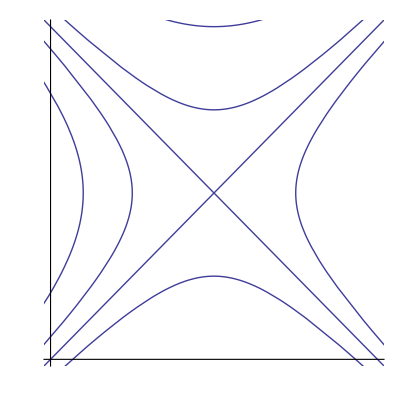

```mathematica
PhasePlot[{-(y-1),-(x-1)},{{0.2,1},{0.5,1},{1,0.5},{1,1},{1,1.5},{1.5,1},{2.3,1},{1,2},{1,2.5},{1.05,1.05},{0.95,1.05},{1.05,0.95},{0.95,0.95}},12,Ticks->False,PlotRange->{{0,2},{0,2}}]
```

```mathematica
Export["/tmp/ode7_2b.eps",%]
```

/tmp/ode7_2b.eps

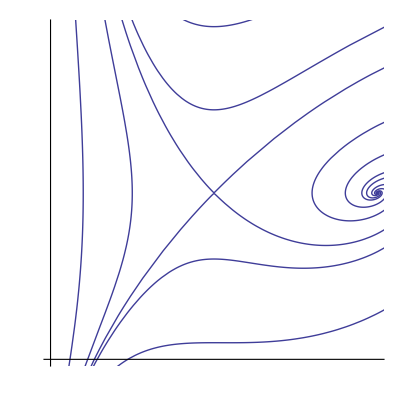

```mathematica
pp1=PhasePlot[{(1-y)x,(1-x)y+(x-1)^2},{{0.2,1},{0.5,1},{1,0.1},{1,1},{1,1.5},{1.6,1},{2.3,1},{1,2},{1,2.5},{1.02,0.98},{1.02,1.02}},12,Ticks->False,PlotRange->{{0,2},{0,2}}]
```

```mathematica
Export["/tmp/ode7_2a.eps",%]
```

/tmp/ode7_2a.eps

### RLC circuit

```mathematica
sol=Simplify[DSolve[{x''[t]+4x'[t] +x[t]==0,x[0]==1,x'[0]==1},x[t],t][[1]]]
```

{x[t]→1/2 ⅇ^(-(2+√3) t) (1-√3+(1+√3) ⅇ^(2 √3 t))}

```mathematica
Plot[x[t]/.sol,{t,0,12},Ticks->None,PlotLabel->"over damping"]
```

```mathematica
sol=Simplify[DSolve[{x''[t]+2x'[t] +x[t]==0,x[0]==1,x'[0]==1},x[t],t][[1]]]
```

{x[t]→ⅇ^-t (1+2 t)}

```mathematica
Plot[x[t]/.sol,{t,0,12},Ticks->None,PlotLabel->"critical damping"]
```

```mathematica
sol=Simplify[DSolve[{x''[t]+x'[t] /2+x[t]==0,x[0]==1,x'[0]==1},x[t],t][[1]]]
```

{x[t]→1/3 ⅇ^(-t/4) (3 Cos[(√15 t)/4]+√15 Sin[(√15 t)/4])}

```mathematica
Plot[x[t]/.sol,{t,0,12},Ticks->None,PlotLabel->"under damping"]
```

### Mathieu

```mathematica
MathieuEq[δ_,ϵ_]={x'[t]==v[t],v'[t]==- δ^2(1+ϵ Cos[t])x[t]};
```

```mathematica
spur[δ_?NumericQ,ϵ_?NumericQ]:=Block[{t,c,sp, ivp},
ivp=Flatten[{MathieuEq[δ,ϵ],x[0]==1,v[0]==0}];
c=(x[t] /.Flatten[NDSolve[ivp,{x[t],v[t]},{t,0,2π}]]) /. t->2π;
ivp=Flatten[{MathieuEq[δ,ϵ],x[0]==0,v[0]==1}];
sp=(v[t] /.Flatten[NDSolve[ivp,{x[t],v[t]},{t,0,2π}]]) /. t->2π;
(c+sp)/2
];
```

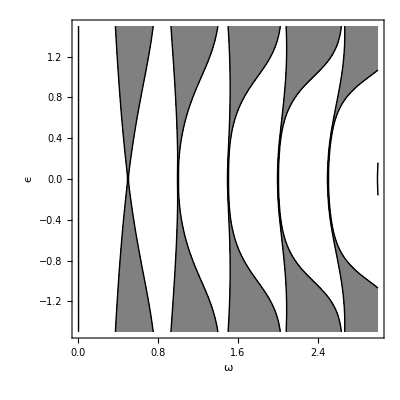

```mathematica
ContourPlot[spur[ω,ϵ]^2,{ω,0,3},{ϵ,-1.5,1.5},PlotPoints->70,AspectRatio->1,ContourShading->{None,Gray},Contours->{0.999},ClippingStyle->Automatic,ContourStyle->Black,FrameLabel->Automatic]
```

```mathematica
Export["ode3_7.eps",%];
```

### Periodic

```mathematica
DSolve[x''[t]+x[t]==Cos[α t],x[t],t]//FullSimplify
```

{{x[t]→C[1] Cos[t]-Cos[t α]/(-1+α^2)+C[2] Sin[t]}}

```mathematica
DSolve[x''[t]+x[t]==Cos[t],x[t],t]//FullSimplify
```

{{x[t]→1/2 (Cos[t]+2 C[1] Cos[t]+t Sin[t]+2 C[2] Sin[t])}}

Quantum mechanics of an electron in a crystal

```mathematica
Φ[z_,t_]:=({{Cos[√z t], Sin[√z t]/(√z)}, {-√z Sin[√z t], Cos[√z t]}});
```

```mathematica
Φ[z,1]//MatrixForm
```

(Cos[√z] | Sin[√z]/(√z)
-√z Sin[√z] | Cos[√z])

```mathematica
Φ[z,1][[1,2]]//MatrixForm
```

Sin[√z]/(√z)

```mathematica
FullSimplify[1/2 Tr[Φ[z,1]]]
```

Cos[√z]

```mathematica
M[z_]=FullSimplify[Φ[z-50,1/2].Φ[z,1/2]];
```

```mathematica
Δ[z_]=FullSimplify[1/2 Tr[M[z]]]
```

(√(-50+z) √z Cos[(√(-50+z))/2] Cos[(√z)/2]-(-25+z) Sin[(√(-50+z))/2] Sin[(√z)/2])/(√(-50+z) √z)

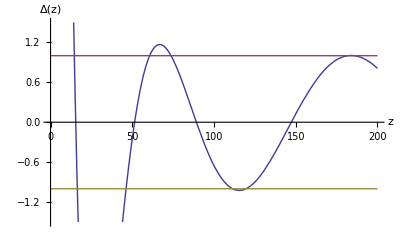

```mathematica
Plot[{Δ[z],1,-1},{z,0,200},PlotRange->{-1.5,1.5},AxesLabel->{"z","Δ(z)"}]
```

```mathematica
ρp[z_]=If[Abs[Δ[z]+√(Δ[z]^2-1)]<1,Δ[z]-√(Δ[z]^2-1),Δ[z]+√(Δ[z]^2-1)];
ρm[z_]=If[Abs[Δ[z]+√(Δ[z]^2-1)]<1,Δ[z]+√(Δ[z]^2-1),Δ[z]-√(Δ[z]^2-1)];
mp[z_]=(ρp[z]-M[z][[1,1]])/(M[z][[1,2]]);
mm[z_]=(ρm[z]-M[z][[1,1]])/(M[z][[1,2]]);
```

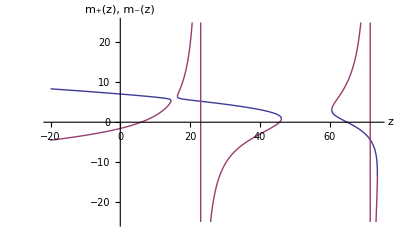

```mathematica
gr1=Plot[{Re[mp[z]],Re[mm[z]]},{z,-20,14.59},PlotPoints->200];
gr2=Plot[{Re[mp[z]],Re[mm[z]]},{z,16.35,46.3},PlotPoints->200,PlotRange->{-25,25}];
gr3=Plot[{Re[mp[z]],Re[mm[z]]},{z,60.6,73.75},PlotPoints->200,PlotRange->{-25,25}];
Show[gr1,gr2,gr3,PlotRange->All,AxesLabel->{"z","m_+(z), m_-(z)"}]
```

```mathematica
sol=Flatten[Solve[{√z== a + ϵ,√(z-1)== a - ϵ},{a,ϵ}]]
```

{a→1/2 (√(-1+z)+√z),ϵ→1/2 (-√(-1+z)+√z)}

```mathematica
ϵ ==1/(4 a) /. sol//Simplify
```

True

```mathematica
Delta[a_,ϵ_]=FullSimplify[1/2 Tr[Φ[(a-ϵ)^2,1/2].Φ[(a+ϵ)^2,1/2]]]
```

(a^2 Cos[a]-ϵ^2 Cos[ϵ])/(a^2-ϵ^2)

```mathematica
Simplify[Delta[2n π,1/(8 n π)],n∈Integers]
```

(256 n^4 π^4-Cos[1/(8 n π)])/(-1+256 n^4 π^4)

```mathematica
Series[% ,{n,∞,6}]  //Simplify
```

1+(1/n)^6/(32768 π^6)+O[1/n]^7

```mathematica
Simplify[Delta[(2n+1) π,1/(4(2 n+1)π)],n∈Integers]
```

-(16 (π+2 n π)^4+Cos[1/(4 π+8 n π)])/(-1+16 (π+2 n π)^4)

```mathematica
Series[%,{n,∞,4}]  //Simplify
```

-1-(1/n)^4/(128 π^4)+O[1/n]^5

### Complex systems, power series

This section requires the package DiscreteMath'DiffEqs' available from
	 http://www.mat.univie.ac.at/~gerald/ftp/book-jac/DiffEqs.m
It needs to be  stored in the Applications/DiscreteMath subfolder of your Mathematica folder. On multi-user systems, you can install an add-on either in the central Mathematica directory (provided you have access to it) or else in your individual user's Mathematica directory (usually ~/.Mathematica/). (You can also put them  somewhere else, as long as you change the $Path variable in Mathematica such that the files can be found by Mathematica or evaluate the packages before using this  notebook.)

#### Riccati

```mathematica
Needs["DiscreteMath`DiffEqs`"]
```

```mathematica
RiccatiEqn[f_]:=D[f, z]  + f^2-z;
```

```mathematica
f[z_]:=SymbSum[h[j] z^j,{j,0,∞}];
h[0]:=h0;h[j_]:=0 /; (j<0);
```

```mathematica
eqn=RiccatiEqn[f[z]]
```

-z+(∑^⋆)_(j=0)^∞j z^(-1+j) h[j]+((∑^⋆)_(j=0)^∞z^j h[j])^2

```mathematica
FactorSum[SplitSum[ShiftPowers[ExpandSum[CauchyProduct[eqn]],z],0]] //Simplify
```

-z+(∑^⋆)_(j=0)^∞z^j ((1+j) h[1+j]+(∑^⋆)_(m1=0)^j h[j-m1] h[m1])

#### Linear

```mathematica
Needs["DiscreteMath`DiffEqs`"]
```

```mathematica
MySeries[f_,{z_,z0_}]:= Block[{ff},
ff[j_]=FullSimplify[SeriesCoefficient[f,{z,z0,j}],j∈Integers&&j≥0];
SymbSum[ff[j] z^j,{j,0,∞}]
];
```

```mathematica
g[z_]=MySeries[1/(1-z),{z,0}]
```

(∑^⋆)_(j=0)^∞z^j

```mathematica
LinearEqn[f_]:=D[f, z]  + f-g[z];
```

```mathematica
f[z_]:=SymbSum[h[j] z^j,{j,0,∞}];
h[0]:=h0;h[j_]:=0 /; (j<0);
```

```mathematica
eqn=LinearEqn[f[z]]
```

-(∑^⋆)_(j=0)^∞z^j+(∑^⋆)_(j=0)^∞j z^(-1+j) h[j]+(∑^⋆)_(j=0)^∞z^j h[j]

```mathematica
FactorSum[SplitSum[ShiftPowers[ExpandSum[eqn],z],0]] //Simplify
```

(∑^⋆)_(j=0)^∞z^j (-1+h[j]+(1+j) h[1+j])

```mathematica
RSolve[-1+h[j]+(1+j) h[1+j]==0,h[j],j]//FullSimplify[#,j∈Integers&&j≥0]&
```

{{h[j]→1/(j!)(-1)^j (-C[1]+ⅇ ExpIntegralEi[-1]+(-1)^j ⅇ ExpIntegralE[1+j,1] j!)}}

#### Linear 2

```mathematica
Needs["DiscreteMath`DiffEqs`"]
```

```mathematica
LinearEqn[f_]:=D[f, z,z]  + (1-z^2)f;
```

```mathematica
f[z_]:=SymbSum[h[j] z^j,{j,0,∞}];
h[j_]:=0 /; (j<0);
```

```mathematica
eqn=LinearEqn[f[z]]
```

(∑^⋆)_(j=0)^∞(-1+j) j z^(-2+j) h[j]+(1-z^2) (∑^⋆)_(j=0)^∞z^j h[j]

```mathematica
FactorSum[SplitSum[ShiftPowers[ExpandSum[eqn],z],0]] //FullSimplify
```

-(∑^⋆)_(j=0)^∞z^j (h[-2+j]-h[j]-(1+j) (2+j) h[2+j])

```mathematica
Clear[h]
```

```mathematica
RSolve[{h[-2+j]-h[j]-(1+j) (2+j) h[2+j]==0,h[-2]==0,h[-1]==0,h[0]==1,h[1]==0},h[j],j]
```

RSolve[{h[-2+j]-h[j]-(1+j) (2+j) h[2+j]==0,h[-2]==0,h[-1]==0,h[0]==1,h[1]==0},h[j],j]

```mathematica
RSolve[{h[-1+j]-h[j]-(1+2j) (2+2j) h[1+j]==0,h[0]==1,h[-1]==0},h[j],j]
```

{{h[j]→(-1/2)^j/Gamma[1+j]}}

#### Bessel

```mathematica
Needs["DiscreteMath`DiffEqs`"]
```

```mathematica
BesselEqn[f_]:=z^2 D[f, z,z]+z D[f, z]  + (z^2- ν^2 )f;
```

```mathematica
u[z_]:=SymbSum[h[j] z^(j+ν),{j,0,∞}];
h[0]:=1; h[j_]:=0 /; (j<0);
```

```mathematica
eqn=BesselEqn[u[z]]
```

(z^2-ν^2) (∑^⋆)_(j=0)^∞z^(j+ν) h[j]+z (∑^⋆)_(j=0)^∞z^(-1+j+ν) (j+ν) h[j]+z^2 (∑^⋆)_(j=0)^∞z^(-2+j+ν) (-1+j+ν) (j+ν) h[j]

```mathematica
ShiftPowers[ExpandSum[ z^-ν eqn],z]
```

(∑^⋆)_(j=2)^∞z^j h[-2+j]+(∑^⋆)_(j=0)^∞-j z^j h[j]+(∑^⋆)_(j=0)^∞j z^j h[j]+(∑^⋆)_(j=0)^∞j^2 z^j h[j]+(∑^⋆)_(j=0)^∞-z^j ν h[j]+(∑^⋆)_(j=0)^∞z^j ν h[j]+(∑^⋆)_(j=0)^∞2 j z^j ν h[j]+(∑^⋆)_(j=0)^∞-z^j ν^2 h[j]+(∑^⋆)_(j=0)^∞z^j ν^2 h[j]

```mathematica
SplitSum[%,0] // FactorSum //Simplify
```

(∑^⋆)_(j=0)^∞z^j (h[-2+j]+j (j+2 ν) h[j])

```mathematica
hh[j_]=hh[j] /. Flatten[RSolve[{hh[j-1]+4j (j+ ν) hh[j]==0,hh[0]==1},hh[j],j]]
```

((-1/4)^j Gamma[1+ν])/(Gamma[1+j] Gamma[1+j+ν])

```mathematica
v[z_]:=SymbSum[g[j] z^(j-ν)+ c Log[z] h[j] z^(j+ν),{j,0,∞}];
g[0]:=1; g[j_]:=0 /; (j<0);
```

```mathematica
eqn=BesselEqn[v[z]] /. Log[z]->0
```

(z^2-ν^2) (∑^⋆)_(j=0)^∞z^(j-ν) g[j]+z (∑^⋆)_(j=0)^∞z^(-1+j-ν) (j-ν) g[j]+c z^(-1+j+ν) h[j]+z^2 (∑^⋆)_(j=0)^∞z^(-2+j-ν) (-1+j-ν) (j-ν) g[j]+c z^(-2+j+ν) (-1+j+ν) h[j]+c z^(-2+j+ν) (j+ν) h[j]

```mathematica
FactorSum[%]//Simplify
```

(∑^⋆)_(j=0)^∞z^(j-ν) ((j^2+z^2-2 j ν) g[j]+2 c z^(2 ν) (j+ν) h[j])

```mathematica
Unprotect[IntegerQ];
IntegerQ[2ν]=True;
```

```mathematica
ShiftPowers[ExpandSum[ z^ν eqn],z]
```

(∑^⋆)_(j=2)^∞z^j g[-2+j]+(∑^⋆)_(j=0)^∞-j z^j g[j]+(∑^⋆)_(j=0)^∞j z^j g[j]+(∑^⋆)_(j=0)^∞j^2 z^j g[j]+(∑^⋆)_(j=0)^∞-z^j ν g[j]+(∑^⋆)_(j=0)^∞z^j ν g[j]+(∑^⋆)_(j=0)^∞-2 j z^j ν g[j]+(∑^⋆)_(j=0)^∞-z^j ν^2 g[j]+(∑^⋆)_(j=0)^∞z^j ν^2 g[j]+(∑^⋆)_(j=2 ν)^∞-c z^j h[j-2 ν]+(∑^⋆)_(j=2 ν)^∞c z^j h[j-2 ν]+(∑^⋆)_(j=2 ν)^∞2 c z^j (j-2 ν) h[j-2 ν]+(∑^⋆)_(j=2 ν)^∞2 c z^j ν h[j-2 ν]

```mathematica
SplitSum[%,0] // FactorSum //Simplify
```

2 c (∑^⋆)_(j=2 ν)^-1 z^j (j-ν) h[j-2 ν]+(∑^⋆)_(j=0)^∞z^j (g[-2+j]+j (j-2 ν) g[j]+2 c (j-ν) h[j-2 ν])

```mathematica
RSolve[{gg[-1+j]+4 j (j+ν) gg[j]+2 c (2 j+ν) hh[j]==0,gg[1]==1},gg[j],j]
```

{{gg[j]→-1/(Gamma[1+j] Gamma[1+j+ν])(-1)^j 2^(-1-2 j) (-c Gamma[1+ν]+c EulerGamma Gamma[1+ν]+8 Gamma[2+ν]+c Gamma[1+ν] PolyGamma[0,1+j]-c Gamma[1+ν] PolyGamma[0,2+ν]+c Gamma[1+ν] PolyGamma[0,1+j+ν])}}

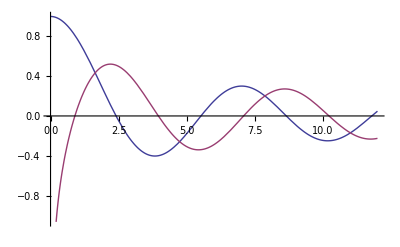

```mathematica
Plot[{BesselJ[0,z],BesselY[0,z]},{z,0,12}]
```

```mathematica
z(BesselJ[n,z]D[BesselY[n,z],z] -D[BesselJ[n,z],z]BesselY[n,z] )//FullSimplify
```

2/π

```mathematica
Sum[2k+ν,{k,1,n-1}]
```

(-1+n) n+(-1+n) ν

#### Legendre

```mathematica
Needs["DiscreteMath`DiffEqs`"]
```

```mathematica
LegendreEqn[f_]:=(1-z^2) D[f, z,z]-2z D[f, z]  + n(n+1)f;
```

```mathematica
u[z_]:=SymbSum[h[j] z^j,{j,0,∞}];
h[0]:=1; h[j_]:=0 /; (j<0);
```

```mathematica
eqn=LegendreEqn[u[z]]
```

(1-z^2) (∑^⋆)_(j=0)^∞(-1+j) j z^(-2+j) h[j]-2 z (∑^⋆)_(j=0)^∞j z^(-1+j) h[j]+n (1+n) (∑^⋆)_(j=0)^∞z^j h[j]

```mathematica
ShiftPowers[ExpandSum[  eqn],z]
```

(∑^⋆)_(j=0)^∞-2 j z^j h[j]+(∑^⋆)_(j=0)^∞j z^j h[j]+(∑^⋆)_(j=0)^∞-j^2 z^j h[j]+(∑^⋆)_(j=0)^∞n z^j h[j]+(∑^⋆)_(j=0)^∞n^2 z^j h[j]+(∑^⋆)_(j=-2)^∞-(2+j) z^j h[2+j]+(∑^⋆)_(j=-2)^∞(2+j)^2 z^j h[2+j]

```mathematica
SplitSum[%,0] // FactorSum //Simplify
```

-(∑^⋆)_(j=0)^∞z^j ((j+j^2-n (1+n)) h[j]-(2+3 j+j^2) h[2+j])

### Planar dynamical systems

```mathematica
Off[General::spell1];
```

This command will generate the phase plot of a planar vector field. The first argument f is the
vector field. The second is a list of initial conditions. The third is the maximal time for which the solution will be computed. In addition there are some optional graphics arguments which are passed to the Show[] command.

```mathematica
Needs["VectorFieldPlots`"];
```

```mathematica
PhasePlot[f_,ic_,tmax_,opts___]:=Block[{i,n=Length[ic],ff,ivp,sol,t1,t2,phaseplot,pvf,vf,vfr,pev,a,ev,evs,optss},
ff=f /. {x->x[t],y->y[t]};
pfv=VectorField /. {opts,VectorField->False};
pev=EigenVectors /. {opts,EigenVectors->False};
optss=DeleteCases[{opts},VectorField->_];
optss=DeleteCases[optss,EigenVectors->_];
optss[[0]]=Sequence;
vf=Graphics[];
ev=Graphics[];
vfr=PlotRange /. {opts, PlotRange->{{-1,1},{-1,1}}};
If[pfv,vf=VectorFieldPlot[f,{x,vfr[[1,1]],vfr[[1,2]]},{y,vfr[[2,1]],vfr[[2,2]]},Frame->False,Axes->True,Ticks->False,PlotPoints->8]];
If[pev,
a=Transpose[{f/. {x->1,y->0},f/. {x->0,y->1}}];
evs=Eigensystem[a][[2]];
If[Im[evs]=={{0,0},{0,0}},
ev=ParametricPlot[evs t,{t,-100,100},PlotStyle->{Red,Red}]];
];
Off[NDSolve::"ndsz"];
Do[
ivp={x'[t]==ff[[1]],y'[t]==ff[[2]],x[0]==ic[[i,1]],y[0]==ic[[i,2]]};
sol=NDSolve[ivp,{x[t],y[t]},{t,-tmax,tmax}];
{t1,t2}=sol[[1]][[1]][[2]][[0]][[1]][[1]];
phaseplot[i]=ParametricPlot[{x[t],y[t]} /. sol,{t,t1,t2}]
,{i,1,n}];
On[NDSolve::"ndsz"];
Show[Table[phaseplot[i],{i,1,n}],vf,ev,optss]
];
```

This command will find all singular points of a vector field. In addition, it will
give the trace and the determinant at each singular point (from which the sing of the
real parts of the eigenvalues can be read off).

```mathematica
Linearize[f_,opts___]:=Block[{sol,i,jac,out,opt},
opt={DetTr,Matrix} /. {opts} /. {DetTr->True,Matrix->False};
jac=Simplify[({{D[f[[1]], x], D[f[[1]], y]}, {D[f[[2]], x], D[f[[2]], y]}})];
sol= Simplify[Solve[{f[[1]]==0,f[[2]]==0},{x,y}]];
Do[
out={{x,y} /.sol[[i]]};
If[opt[[1]],out=Append[out,Simplify[{Tr[jac /. sol[[i]] ],Det[jac /. sol[[i]] ]}]] ];
If[opt[[2]],out=Append[out,Simplify[MatrixForm[jac /. sol[[i]]]]] ];
Print[out]; ,{i,1,Length[sol]}];
];
```

#### Linear equations

Here is the phase plot of a spiral source.

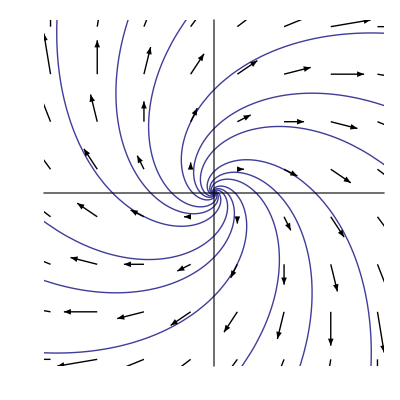

```mathematica
PhasePlot[{x+ y,-x +y},{{1,1},{-1,-1},{-1,1},{1,-1},{2,2},{-2,-2},{-2,2},{2,-2},{3,3},{-3,-3},{-3,3},{3,-3}},5,PlotRange->{{-5,5},{-5,5}},Ticks->False,VectorField->True]
```

```mathematica
Export["ode3_1a.eps",%];
```

and of a spiral sink.

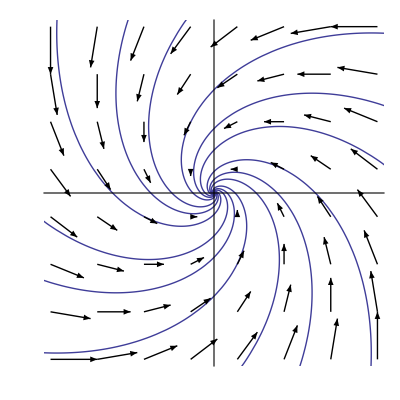

```mathematica
PhasePlot[{-x- y,x -y},{{1,1},{-1,-1},{-1,1},{1,-1},{2,2},{-2,-2},{-2,2},{2,-2},{3,3},{-3,-3},{-3,3},{3,-3}},5,PlotRange->{{-5,5},{-5,5}},Ticks->False,VectorField->True]
```

```mathematica
Export["ode3_1b.eps",%];
```

No spiral part

```mathematica
MatrixForm[JordanDecomposition[({{1, 1.5}, {0.5, 1}})][[2]]]
```

(1.86603 | 0
0 | 0.133975)

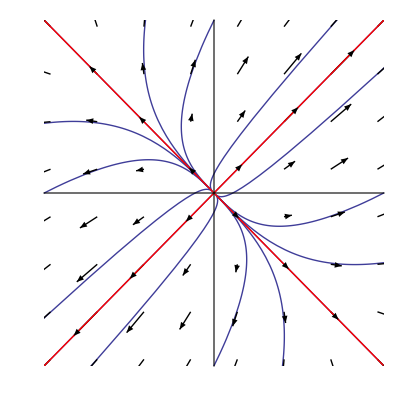

```mathematica
PhasePlot[{x+0.5y,0.5x +y},{{1,1},{-1,-1},{-1,1},{1,-1},{2,1},{2,-1},{-2,1},{-2,-1},{1,2},{1,-2},{-1,2},{-1,-2},{3,-2},{2,-3},{-3,2},{-2,3}},5,PlotRange->{{-5,5},{-5,5}},Ticks->False,VectorField->True,EigenVectors->True]
```

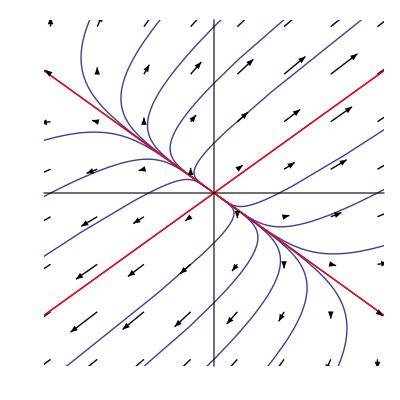

```mathematica
PhasePlot[{x+ y,0.5x +y},{{0.8164965809277261,0.5773502691896258},{0,1.5},{0,3.3},{0,5},{0,7},{0,10},{0,50},{-2,0},{-5,0},{-9,0},{-0.8164965809277261,-0.5773502691896258},{0,-1.5},{0,-3.3},{0,-5},{0,-7},{0,-10},{0,-50},{2,0},{5,0},{9,0}},10,PlotRange->{{-5,5},{-5,5}},Ticks->False,VectorField->True,EigenVectors->True]
```

```mathematica
Export["ode3_2a.eps",%];
```

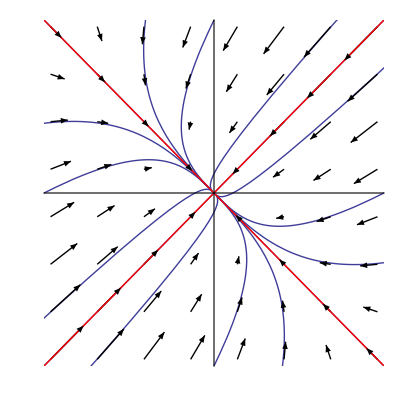

```mathematica
PhasePlot[{-x- 0.5y,-0.5x -y},{{1,1},{-1,-1},{-1,1},{1,-1},{2,1},{2,-1},{-2,1},{-2,-1},{1,2},{1,-2},{-1,2},{-1,-2},{3,-2},{2,-3},{-3,2},{-2,3}},5,PlotRange->{{-5,5},{-5,5}},Ticks->False,VectorField->True,EigenVectors->True]
```

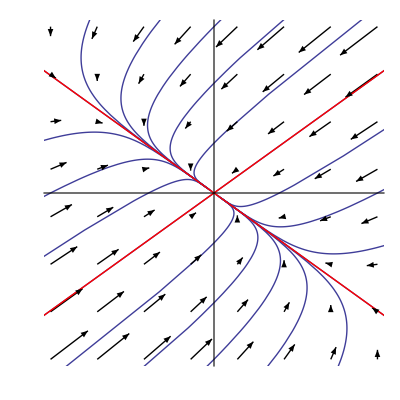

```mathematica
PhasePlot[{-x- y,-0.5x -y},{{0.8164965809277261,0.5773502691896258},{0,1.5},{0,3.3},{0,5},{0,7},{0,10},{0,50},{-2,0},{-5,0},{-9,0},{-0.8164965809277261,-0.5773502691896258},{0,-1.5},{0,-3.3},{0,-5},{0,-7},{0,-10},{0,-50},{2,0},{5,0},{9,0}},10,PlotRange->{{-5,5},{-5,5}},Ticks->False,VectorField->True,EigenVectors->True]
```

```mathematica
Export["ode3_2b.eps",%];
```

And here is the phase plot of a saddle.

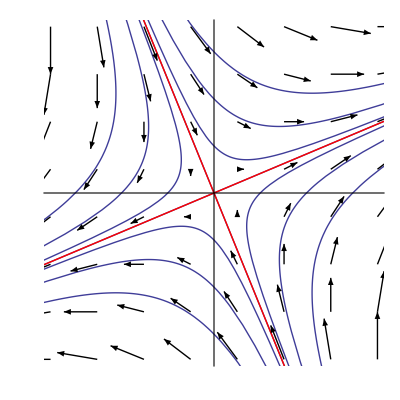

```mathematica
PhasePlot[{x+ y,x -y},{{1-√2,1},{-1+√2,-1},{1+√2,1},{-1-√2,-1},{1,1},{-1,-1},{-1,1},{1,-1},{2,2},{-2,-2},{-2,2},{2,-2},{3,3},{-3,-3},{-3,3},{3,-3}},3,PlotRange->{{-5,5},{-5,5}},Ticks->False,VectorField->True,EigenVectors->True]
```

```mathematica
Export["ode3_3.eps",%];
```

Finally a center

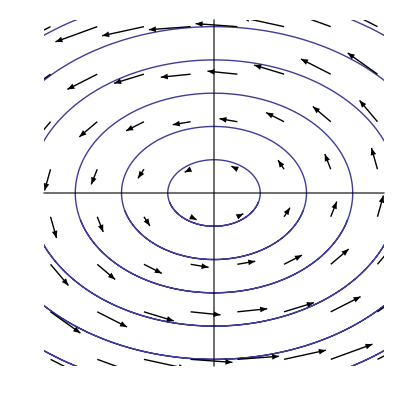

```mathematica
PhasePlot[{- 2y,x },{{0,1},{0,2},{0,3},{0,4},{0,5},{0,6}},π,PlotRange->{{-5,5},{-5,5}},Ticks->False,VectorField->True]
```

```mathematica
Export["ode3_4.eps",%];
```

```mathematica
MatrixForm[JordanDecomposition[({{1, -1}, {1, 3}})][[2]]]
```

(2 | 1
0 | 2)

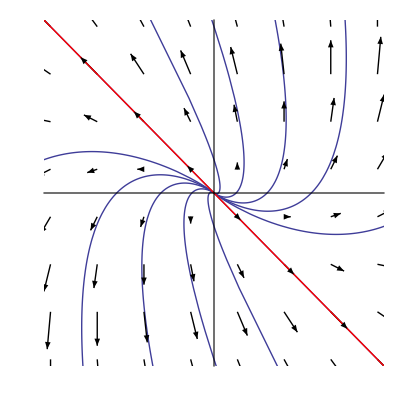

```mathematica
PhasePlot[{x-y,x +3y},{{-1,1},{0,1},{0,5},{0,12},{0,22},{0,50},{1,-1},{0,-1},{0,-5},{0,-12},{0,-22},{0,-50}},6,PlotRange->{{-5,5},{-5,5}},Ticks->False,VectorField->True,EigenVectors->True]
```

```mathematica
Export["ode3_5.eps",%];
```

#### Newton's equations

Here is the potential of the mathematical pendulum.

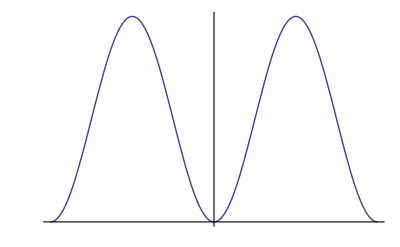

```mathematica
U[x_]=1-Cos[x];Plot[U[x],{x,-2 π,2 π},Ticks->False]
```

Here is the  corresponding vector field.

```mathematica
Needs["VectorFieldPlots`"];
```

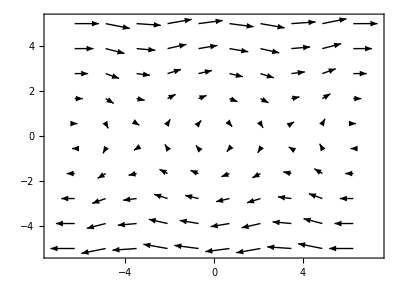

```mathematica
VectorFieldPlot[{y,-U'[x]},{x,-2 π,2 π},{y,-5,5},Frame->True,PlotPoints->10]
```

Here is the correspondign phase plot.

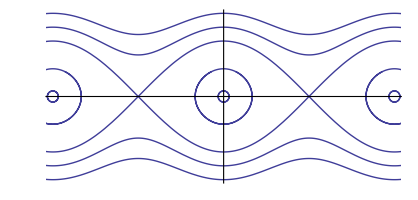

```mathematica
PhasePlot[{y,-U'[x]},{{0,0.2},{0,1},{-2π,0.2},{-2π,1},{2π,0.2},{2π,1},{0,2},{2π,-2},{2π,2},{-2π,-2},{-2π,2},{0,-2},{0,2.5},{0,-2.5},{0,3},{0,-3}},2π,PlotRange->{{-2π,2π},{-3,3}},Ticks->False]
```

Here is another example.

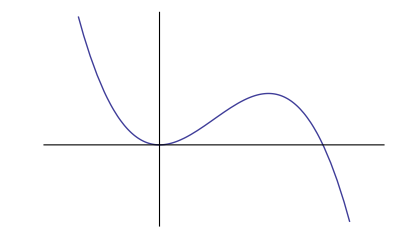

```mathematica
U[x_]=x^2/2- x^3/3;Plot[U[x],{x,-1,2},Ticks->False]
```

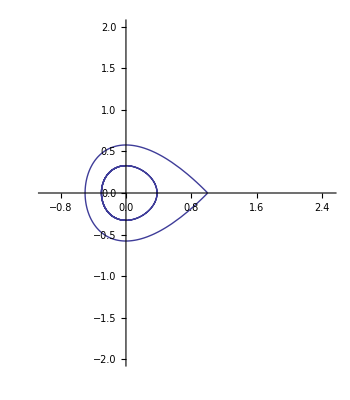

```mathematica
PhasePlot[{y,-U'[x]},{{-1,0},{-0.7,0},{-0.5,0},{-0.3,0},{1.05,0.05},{1.5,0},{2,0}},8,PlotRange->{{-1,2.5},{-2,2}},Ticks->True]
```

```mathematica
Export["/tmp/ode6_5.eps",%]
```

/tmp/ode6_5.eps

#### Ecological models for two species.

```mathematica
Off[NDSolve::ndsz];Off[InterpolatingFunction::dmval];
```

The Volterra-Lotka equations.

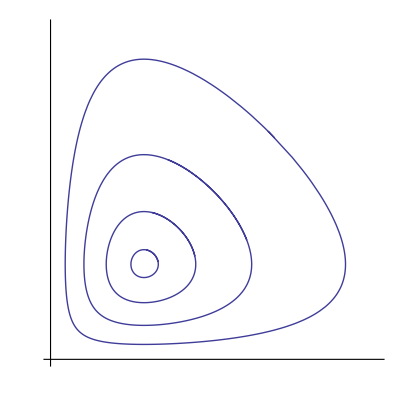

```mathematica
PhasePlot[{(1-y)x,(x-1)y},{{0.3,0.3},{0.5,0.5},{0.7,0.7},{0.9,0.9},{1,1}},3.7,PlotRange->{{0,3.5},{0,3.5}},Ticks->False]
```

The Volterra-Lotka equations with limited growth.

```mathematica
α=1;λ=2;μ=1;xmax=4;ymax=2;
```

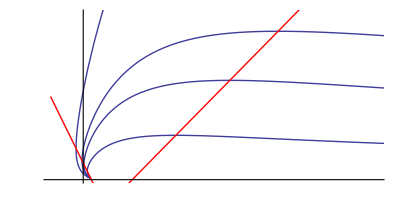

```mathematica
gr1=PhasePlot[{(1-y-λ x) x,α (x-1-μ y) y},{{0.4,1/8},{1,1/2},{1,1},{1,3}},5,Ticks->False];
gr2=Plot[{1-λ x,(x-1)/μ},{x,0,xmax},PlotPoints->30,PlotStyle->RGBColor[1,0,0]];
Show[gr1,gr2,PlotRange->{{0,xmax},{0,ymax}}]
```

```mathematica
α=1;λ=1/2;μ=1;xmax=3;ymax=2;
```

```mathematica
gr1=PhasePlot[{(1-y-λ x) x,α (x-1-μ y) y},{{1/λ,0.001},{0.2,1},{0.6,1},{1,1},{2,1},{2,1/2}},12,Ticks->False];
gr2=Plot[{1-λ x,(x-1)/μ},{x,0,xmax},PlotPoints->30,PlotStyle->RGBColor[1,0,0]];
Show[gr1,gr2,PlotRange->{{0,xmax},{0,ymax}}]
```

The case of competing species.

```mathematica
PhasePlot[{(1-y)x,(1-x)y},{{0.2,1},{0.7,1},{1,0.7},{1,1},{1,1.5},{1.3,1},{2,1}},12,Ticks->False,PlotRange->{{0,3},{0,3}}]
```

The case of competing species with limited growth.

```mathematica
λ=.;μ=.;
Linearize[{(1-y-λ x)x,α(1-x-μ y )y}]
```

{{0,0},{1+α,α}}

{{1/λ,0},{-1+α-α/λ,α (-1+1/λ)}}

{{(-1+μ)/(-1+λ μ),(-1+λ)/(-1+λ μ)},{(α μ-λ (-1+μ+α μ))/(-1+λ μ),(α (-1+λ) (-1+μ))/(-1+λ μ)}}

{{0,1/μ},{1-α-1/μ,α (-1+1/μ)}}

```mathematica
α=1;λ=0.4;μ=0.55;xmax=4;ymax=2;
```

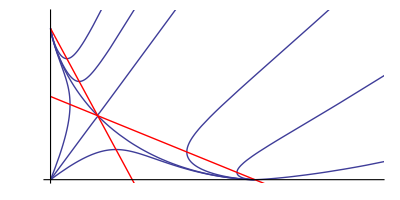

```mathematica
gr1=PhasePlot[{(1-y-λ x) x,α (1-x-μ y) y},{{-(1-μ)/(-1+λ μ),-(1-λ)/(-1+λ μ)-0.01},{-(1-μ)/(-1+λ μ),-(1-λ)/(-1+λ μ)+0.01},{0.2,0.6},{0.3,0.2},{1,2},{0.6,2},{2,0.8},{4,1.2},{4,0.2}},21,Ticks->False];
gr2=Plot[{1-λ x,(1-x)/μ},{x,0,xmax},PlotPoints->30,PlotStyle->RGBColor[1,0,0]];
Show[gr1,gr2,PlotRange->{{0,xmax},{0,ymax}}]
```

```mathematica
α=1;λ=1.5;μ=0.55;xmax=4;ymax=2;
```

```mathematica
gr1=PhasePlot[{(1-y-λ x) x,α (1-x-μ y) y},{{-(1-μ)/(-1+λ μ),-(1-λ)/(-1+λ μ)-0.01},{-(1-μ)/(-1+λ μ),-(1-λ)/(-1+λ μ)+0.01},{0.2,0.6},{0.3,0.2},{1,2},{0.6,2},{2,0.8},{4,1.2},{4,0.2}},21,Ticks->False];
gr2=Plot[{1-λ x,(1-x)/μ},{x,0,xmax},PlotPoints->30,PlotStyle->RGBColor[1,0,0]];
Show[gr1,gr2,PlotRange->{{0,xmax},{0,ymax}}]
```

#### The van der Pol equation:

```mathematica
f[x_]=1(x^3/3-x);
PhasePlot[{y- f[x],-x},{{0,0.1},{0,2.8},{0,-0.1},{0,-2.9}},9,Ticks->False,PlotRange->{{-3,3},{-3,3}}]
```

```mathematica
PhasePlot[{y,(1-x^2)y-x},{{0,0.1},{0,2.8},{0,-0.1},{0,-2.9}},9,Ticks->False,PlotRange->{{-3,3},{-3.5,3.5}}]
```

#### Hopf bifurcation

```mathematica
f[x]=x^3/3-μ x;
```

```mathematica
μ=-1;
PhasePlot[{y- f[x],-x},{{0,0.1},{0,2.8},{0,-0.1},{0,-2.9}},9,Ticks->False,PlotRange->{{-3,3},{-3,3}}]
```

```mathematica
μ=0;
PhasePlot[{y- f[x],-x},{{0,2.8},{0,-2.9}},100,Ticks->False,PlotRange->{{-3,3},{-3,3}}]
```

```mathematica
μ=1;
PhasePlot[{y- f[x],-x},{{0,0.1},{0,2.8},{0,-0.1},{0,-2.9}},9,Ticks->False,PlotRange->{{-3,3},{-3,3}}]
```

#### Logistic equation with periodic harvesting

```mathematica
x[t] /. DSolve[{x'[t]== x[t](1-x[t]),x[0]==x0},x[t],t][[1]] /. t->1
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

(ⅇ x0)/(1-x0+ⅇ x0)

```mathematica
p[x0_,h_]:= Block[{sol,x,t},sol=x /.NDSolve[{x'[t]==x[t](1-x[t])-h(1+Sin[2π t]),x[0]==x0},x,{t,0,1}][[1]];
sol[1] 
]
```

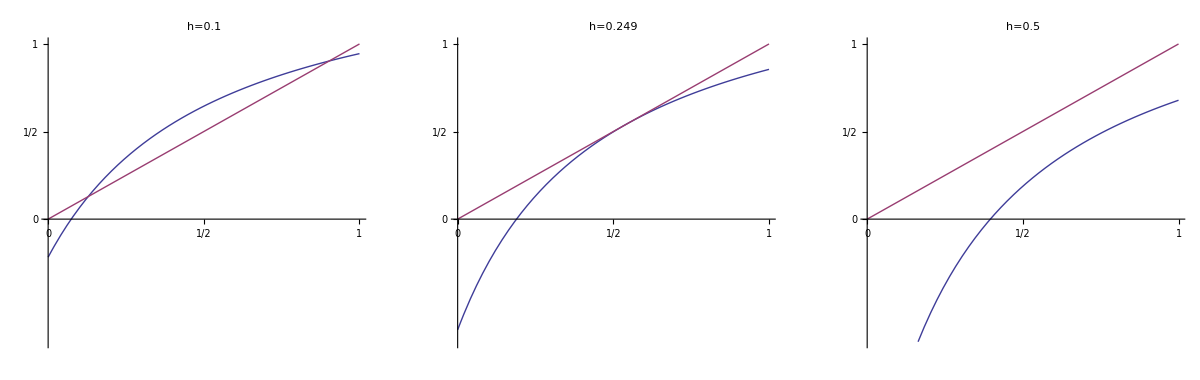

```mathematica
GraphicsRow[{Plot[{p[x,0.1],x},{x,0,1},Ticks->{{0,1/2,1},{0,1/2,1}},PlotRange->{-0.7,1},PlotLabel->"h=0.1",AspectRatio->1],Plot[{p[x,0.249],x},{x,0,1},Ticks->{{0,1/2,1},{0,1/2,1}},PlotRange->{-0.7,1},PlotLabel->"h=0.249",AspectRatio->1],Plot[{p[x,0.5],x},{x,0,1},Ticks->{{0,1/2,1},{0,1/2,1}},PlotRange->{-0.7,1},PlotLabel->"h=0.5",AspectRatio->1]}]
```

```mathematica
Export["ode1_6.eps",%]
```

ode1_6.eps

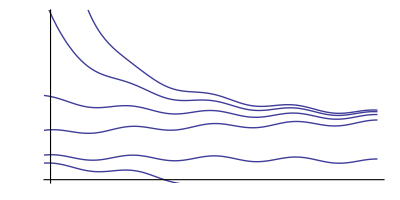

```mathematica
PhasePlot[{1,y(1-y)-0.2(1+Sin[2π x])},{{0,0.2},{0,0.3},{0,0.6},{0,1},{0,2},{0,6}},4,PlotRange->{{0,4},{0,2}},Ticks->False]
```

```mathematica
Export["ode.eps",%]
```

ode.eps

### The Lorenz system

```mathematica
tmax=20;σ=10;ρ=28;β=8/3;orbit=NDSolve[{x'[t]==-σ (x[t]-y[t]),y'[t]==-x[t] z[t]+ρ x[t]-y[t],z'[t]==x[t] y[t]-β z[t],x[0]==30,y[0]==10,z[0]==40},{x,y,z},{t,0,tmax},MaxSteps->5000];
gr=ParametricPlot3D[Evaluate[{x[t],y[t],z[t]}/.orbit],{t,0,tmax},PlotPoints->2000,Axes->False,PlotRange->All]
```

-Graphics3D-

```mathematica
Show[gr,Graphics3D[{RGBColor[0,0,1],PointSize[0.01],Point[{-√(β (ρ-1)),-√(β (ρ-1)),ρ-1}],Point[{√(β (ρ-1)),√(β (ρ-1)),ρ-1}]}]]
```

```mathematica
Clear[σ,ρ,β]
```

```mathematica
f[x_,y_,z_]:={-σ (x-y),ρ x-x z-y,x y-β z};
```

```mathematica
jac=Simplify[({{D[f[x,y,z][[1]], x], D[f[x,y,z][[1]], y], D[f[x,y,z][[1]], z]}, {D[f[x,y,z][[2]], x], D[f[x,y,z][[2]], y], D[f[x,y,z][[2]], z]}, {D[f[x,y,z][[3]], x], D[f[x,y,z][[3]], y], D[f[x,y,z][[3]], z]}})] ;
```

```mathematica
MatrixForm[jac]
```

(-σ | σ | 0
-z+ρ | -1 | -x
y | x | -β)

```mathematica
MatrixForm[jac/. {x->0,y->0,z->0}]
```

(-σ | σ | 0
ρ | -1 | 0
0 | 0 | -β)

```mathematica
Eigenvalues[jac /. {x->0,y->0,z->0}]//FullSimplify
```

{-β,1/2 (-1-σ-√(1+σ (-2+4 ρ+σ))),1/2 (-1-σ+√(1+σ (-2+4 ρ+σ)))}

```mathematica
MatrixForm[jac/. {x->√(β(ρ-1)),y->√(β(ρ-1)),z->ρ-1}]
```

(-σ | σ | 0
1 | -1 | -√(β (-1+ρ))
√(β (-1+ρ)) | √(β (-1+ρ)) | -β)

```mathematica
σ=10;ρ=470/19; β=8/3;
```

```mathematica
Eigenvalues[jac/. {x->√(β(ρ-1)),y->√(β(ρ-1)),z->ρ-1}]//N
```

{-13.6667,0.-9.62453 ⅈ,0.+9.62453 ⅈ}

### The logistic map

```mathematica
ShowWeb[f_,xstart_,nmax_,opts___]:=Module[{x,xmin,xmax,delta,graph,web,lines},
lines=Type /. {opts,Type->Line};
x[0]:=xstart;
x[n_]:=x[n]=f[x[n-1]];
If[x[0]==x[1],Return[Print["Fixed Point!"]]];
web=Flatten[Table[{{x[n],x[n]},{x[n],x[n+1]}},{n,0,nmax}],1];
xmax=Max[web];xmin=Min[web];delta=0.1(xmax-xmin);
graph=Plot[{f[x],x},{x,xmin-delta,xmax+delta}];
Show[graph,Graphics[lines[web]]]
] /;(IntegerQ[nmax]&&Positive[nmax])
```

```mathematica
Arrows[l_List]:={Arrowheads[Small],Table[Arrow[{l[[i]],l[[i+1]]}],{i,Length[l]-1}]};
```

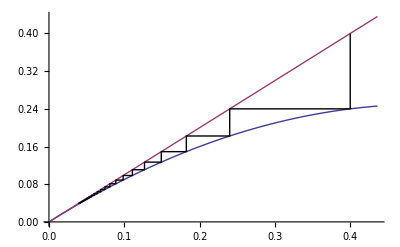

```mathematica
ShowWeb[1#(1-#)&,0.4,20]
```

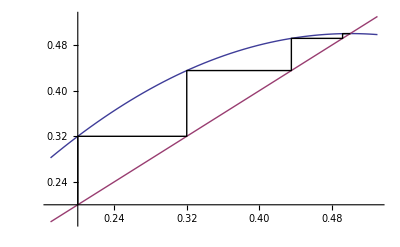

```mathematica
ShowWeb[2#(1-#)&,0.2,20]
```

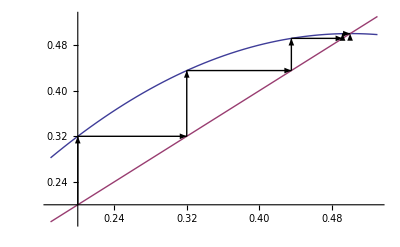

```mathematica
ShowWeb[2#(1-#)&,0.2,4,Type->Arrows]
```

```mathematica
ShowWeb[3.1#(1-#)&,0.4,20];
```

```mathematica
Solve[μ x(1-x)==x,x]
```

{{x→0},{x→(-1+μ)/μ}}

```mathematica
Solve[-(-1+x) x μ^2 (1-x μ+x^2 μ)==x,x]//FullSimplify
```

{{x→0},{x→(-1+μ)/μ},{x→(1+μ-√((-3+μ) (1+μ)))/(2 μ)},{x→(1+μ+√((-3+μ) (1+μ)))/(2 μ)}}

```mathematica
BifurcationList[f_,x0_,{μ_,μ0_,μ1_},opts___]:=
Block[{Nmin,Nmax,Steps,Delta,mychop},
{Nmin,Nmax,Steps,Delta}={Nmin,Nmax,Steps,Delta} /. {opts} /. {Nmin->300,Nmax->500, Steps->300,Delta->0.002};
If[Delta>0,mychop=Compile[{x},  Evaluate[Round[x /Delta]Delta]],mychop[x_]=Chop[x]];
Flatten[Table[
Module[{x,l},
x=Nest[f,x0,Nmin];
l=NestList[f,x,Nmax-Nmin];
l=Map[mychop,l];
l=Union[l];
Map[{μ,#}&,l] ],
{μ,μ0,μ1,(μ1-μ0)/Steps}],1]
];
```

```mathematica
list=BifurcationList[μ#(1-#)&,0.4,{μ,2.95,4.}];
```

```mathematica
Length[list]
```

15433

```mathematica
StripBifurcationList[list_,del_]:=Block[{d,l1,l2},
l1=Transpose[list][[1]];
l2=Transpose[list][[2]];
d=(Max[l2]-Min[l2])/del;
Union[Transpose[{l1,Map[d Round[#/d]&,l2]}]]
]
```

```mathematica
Length[list=StripBifurcationList[list,300]]
```

12739

```mathematica
ListPlot[list,PlotStyle->{PointSize[0.002]},PlotRange->All,Axes->False,AspectRatio->0.8]
```

```mathematica
μ=.
```

```mathematica
f[x_]:=μ x (1-x);p=1-1/μ;
```

```mathematica
g[x_]=Nest[f,x,3]
```

(1-x) x μ^3 (1-(1-x) x μ) (1-(1-x) x μ^2 (1-(1-x) x μ))

```mathematica
g[p]
```

1-1/μ

```mathematica
eqn=Simplify[g[x] ==x/. μ->4]
```

-64 (1-2 x)^2 (-1+x) x (1-8 x+8 x^2)^2==x

```mathematica
sol=Simplify[Union[Solve[eqn,x]]]
```

{{x→0},{x→3/4},{x→1/2-1/4 (1/2 (1+ⅈ √3))^(2/3)+1/8 ⅈ (1/2 (1+ⅈ √3))^(1/3) (ⅈ+√3)},{x→1/8 (4+2/(1/2 (1+ⅈ √3))^(1/3)+2^(2/3) (1+ⅈ √3)^(1/3))},{x→1/16 (8-2^(2/3) (1+ⅈ √3)^(4/3)+(2 ⅈ (ⅈ+√3))/(1/2 (1+ⅈ √3))^(1/3))},{x→1/24 (14+(2 7^(2/3))/(1/2 (-1+3 ⅈ √3))^(1/3)+2^(2/3) (-7+21 ⅈ √3)^(1/3))},{x→7/12-((7/2)^(2/3) (1+ⅈ √3))/(12 (-1+3 ⅈ √3)^(1/3))+1/24 ⅈ (7/2 (-1+3 ⅈ √3))^(1/3) (ⅈ+√3)},{x→7/12+((7/2)^(2/3) (-1+ⅈ √3))/(12 (-1+3 ⅈ √3)^(1/3))-1/24 (1+ⅈ √3) (7/2 (-1+3 ⅈ √3))^(1/3)}}

```mathematica
FullSimplify[ComplexExpand[1/24 (14+(2 7^(2/3))/(-1/2+(3 ⅈ √3)/2)^(1/3)+2^(2/3) (-7+21 ⅈ √3)^(1/3))]]
```

1/12 (7+√7 Cos[1/3 ArcTan[3 √3]]+√21 Sin[1/3 ArcTan[3 √3]])

```mathematica
FullSimplify[(1/2 (1+ⅈ √3))^(1/3)]
```

(-1)^(1/9)

```mathematica
FullSimplify[1/8 (4+2/(-1)^(1/9)+2 (-1)^(1/9))]
```

1/4 (2+(-1)^(1/9)-(-1)^(8/9))

```mathematica
FullSimplify[ComplexExpand[%]]
```

1/2 (1+Cos[π/9])

```mathematica
Simplify[f[%] /. μ->4]
```

1-Cos[π/9]^2

```mathematica
Simplify[f[%] /. μ->4]
```

1/4 (2+(-1)^(1/9)-(-1)^(8/9))

```mathematica
N[%]
```

0.969846-6.93889×10^-17 ⅈ

```mathematica
Chop[N[%]]
```

0.969846

```mathematica
f[f[0.6112604669781573]]
```

0.237621 (1-0.237621 μ) μ^2

```mathematica
eqs={x==g[x],g'[x]==1}
```

{x==(1-x) x μ^3 (1-(1-x) x μ) (1-(1-x) x μ^2 (1-(1-x) x μ)),(1-x) x μ^3 (1-(1-x) x μ) (-(1-x) x μ^2 (-(1-x) μ+x μ)-(1-x) μ^2 (1-(1-x) x μ)+x μ^2 (1-(1-x) x μ))+(1-x) x μ^3 (-(1-x) μ+x μ) (1-(1-x) x μ^2 (1-(1-x) x μ))+(1-x) μ^3 (1-(1-x) x μ) (1-(1-x) x μ^2 (1-(1-x) x μ))-x μ^3 (1-(1-x) x μ) (1-(1-x) x μ^2 (1-(1-x) x μ))==1}

```mathematica
sol=Union[Solve[eqs,{x,μ}]];
```

```mathematica
sol[[8]]
```

{x→1/21 (10+√2)-(1/2 (25-22 √2+ⅈ √(43011-29700 √2)))^(1/3)/(3 7^(2/3))+(-9+4 √2)/(3 (7/2 (25-22 √2+ⅈ √(43011-29700 √2)))^(1/3)),μ→1+2 √2}

```mathematica
Chop[N[%]]
```

{x→0.159929,μ→3.82843}

```mathematica
FullSimplify[(1/2 (25-22 √2+ⅈ √(43011-29700 √2)))^(1/3)]
```

(1/2 ⅈ (-25+22 √2) (ⅈ+3 √3))^(1/3)

```mathematica
FullSimplify[1/2^(1/3)(-1+ⅈ 3 √3)^(1/3)(-1+2 √2)]
```

(-1+2 √2) Root[7+#1^3+#1^6&,6]

```mathematica
Simplify[1/21 (10+√2)-((-1+2 √2) (-1/2+(3 ⅈ √3)/2)^(1/3))/(3 7^(2/3))+(-9+4 √2)/(3 7^(1/3)(-1+2 √2) (-1/2+(3 ⅈ √3)/2)^(1/3))]
```

1/42 (2 (10+√2)+(2 7^(2/3) (-9+4 √2))/((-1+2 √2) (1/2 (-1+3 ⅈ √3))^(1/3))+2^(1/6) (-4+√2) (-7+21 ⅈ √3)^(1/3))

```mathematica
Simplify[ComplexExpand[%]]
```

1/(-21+42 √2)(-6+19 √2+√7 (-9+4 √2) Cos[1/3 ArcTan[3 √3]]+√21 (-9+4 √2) Sin[1/3 ArcTan[3 √3]])

```mathematica
FullSimplify[%]
```

1/21 (10+√2+(√7-2 √14) Cos[1/3 ArcTan[3 √3]]+(√21-2 √42) Sin[1/3 ArcTan[3 √3]])

```mathematica
N[%]
```

0.159929

```mathematica
sol=Union[Solve[{y==f[x],z==f[y],x==f[z],f'[x]f'[y]f'[z]==1},{x,y,z,μ}]];
```

```mathematica
Chop[N[sol[[6]]]]
```

{x→0.514355,y→0.956318,z→0.159929,μ→3.82843}

```mathematica
FullSimplify[sol[[6]]]
```

$Aborted

```mathematica
Solve[f[x]==x,x]
```

{{x→0},{x→-√3},{x→√3}}

```mathematica
Simplify[(f[x]-p)/(x-p)]
```

(9-4 x^3)/(9-12 x)

```mathematica
FullSimplify[(f[f[x]]-p)/(x-p)]
```

(27+16 x^3 (-3+x^3))/(27-36 x)

```mathematica
sol=Solve[f[f[x]]==x,x]//FullSimplify
```

{{x→0},{x→Root[9-12 #1^2+4 #1^5&,1]},{x→Root[9-12 #1^2+4 #1^5&,2]},{x→Root[9-12 #1^2+4 #1^5&,3]},{x→Root[9-12 #1^2+4 #1^5&,4]},{x→Root[9-12 #1^2+4 #1^5&,5]}}

```mathematica
D[f[f[x]],x] /.sol//Simplify
```

{0,6-4 Root[9-12 #1^2+4 #1^5&,1]^2,6-4 Root[9-12 #1^2+4 #1^5&,2]^2,6-4 Root[9-12 #1^2+4 #1^5&,3]^2,6-4 Root[9-12 #1^2+4 #1^5&,4]^2,6-4 Root[9-12 #1^2+4 #1^5&,5]^2}

```mathematica
Solve[4+2 μ-μ^2==-1]
```

{}

```mathematica
f[x_]=μ x (1-x);
```

```mathematica
g[y_]=x /.Solve[f[x]==y,x][[1]];
```

```mathematica
g[1] /. μ->4
```

-(-3)^(1/3)

### The tent map

```mathematica
μ=0.9;
F[x_]=μ(1-2Abs[x-1/2]);
F[n_,x_]:=Nest[F,x,n]
```

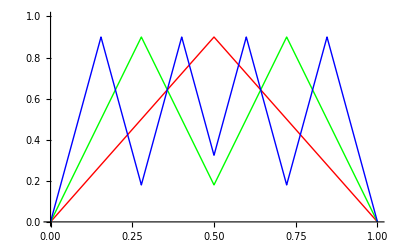

```mathematica
Plot[Evaluate[Table[F[n,x],{n,3}]],{x,0,1},PlotRange->{0,1},PlotStyle->{RGBColor[1,0,0],RGBColor[0,1,0],RGBColor[0,0,1]}]
```

### Homoclinic orbit

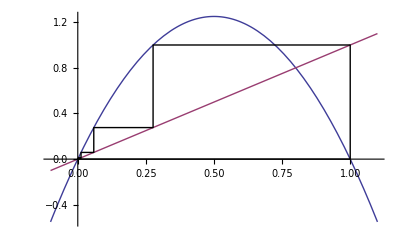

```mathematica
μ=5;
x0=Nest[(1/2- √(1/4- #/μ))&,1.,5];
ShowWeb[μ#(1-#)&,x0,6]
```